## Anderson Neutrino Mass Model for Three Neutrinos.

```mathematica
(e^1)[t_,W_]:=RandomReal[{2*t,2*t+W},{o,o,K,K}] ;K=15;o=3;
(* K is the number of left and right fermion in a single generation and o is the number of generations of clockwork fermion. *)
```

```mathematica
t=1;W=5;
```

```mathematica
fg = (e^1)[t,W];
(* Randomly generating the values of e^ab for different generations and clockwork fermion. *)
```

```mathematica
hk = Table[0,{i,1,o},{j,1,o},{k,1,K},{h,1,K}];
(* Dummy tensor to store the values of e^ab and t^ab *)
```

```mathematica
i=1;While[i<o+1,For[j=1,j<o+1,j++,For[k=1,k<K+1,k++,hk[[i,j,k,k]] = fg[[i,j,k,k]]]];i++]
(* Assigning values e^ab to the elements of dummy tensor hk *)
```

```mathematica
a= Table[Subscript[p, i ,j],{i,1,o},{j,1,o}];
(* Dummy variables to store the values of t^ab , here a and b refers to generation of fermion. *)
```

```mathematica
i=1;While[i<o+1,{j=1;While[j<o+1,Subscript[p, i,j] = t;j++]};i++]
(* Assigning values to these t^ab *)
```

```mathematica
a;
(* Values of t^ab are stored as Subscript[p, a,b] *)
```

```mathematica
i=1;While[i<o+1,For[j=1,j<o+1,j++, For[k=1,k<K,k++,{hk[[i,j,k+1,k]] = a[[i,j]],hk[[i,j,k,k+1]] = a[[i,j]]}]];i++] 
(* Creating the tensor containing e^ab and t^ab as its components, in Subscript[L, i]^a and Subscript[R, j]^b basis. *)
```

```mathematica
hk;
(* Tensor in Subscript[L, i]^a and Subscript[R, j]^b basis. *)
```

### Converting rank 4 tensor hk to rank 2 matrix “mass mat” .

```mathematica
b = Table[Subscript[f, i,j] ,{i,1,o},{j,1,o}]
(* Creating the matrix that will store the elements of tensor hk as its elements *)
```

{{f_(1,1),f_(1,2),f_(1,3)},{f_(2,1),f_(2,2),f_(2,3)},{f_(3,1),f_(3,2),f_(3,3)}}

```mathematica
i=1;While[i<o+1,For[j=1,j<o+1,j++, b[[i,j]] = Table[0,{h,1,K},{l,1,K}]];i++]
(* Assigning dummy values 0 to these created matrix Subscript[b, i,j] *)
```

```mathematica
i=1; While[i<o+1,{j=1; While[j<o+1,For[q=1,q<K+1,q++,For[s=1,s<K+1,s++,b[[i,j]][[q,s]] = hk[[i,j,q,s]] ]];j++]};i++]
(* Assigning elements of hk as values to elements of matrix Subscript[b, i,j] *)
```

```mathematica
j=1;While[j<o+1,{i=2;While[i<o+1,b[[j,i]] = Join[b[[j,i-1]],b[[j,i]],2];i++]};j++]
```

```mathematica
(* Joining these matrix to form a bigger matrix. *)
```

```mathematica
i=2;While[i<o+1,b[[i,o]] = Join[b[[i-1,o]],b[[i,o]]];i++] 
(* Joining these matrix to form the final matrix that is consistent with tensor hk. *)
```

```mathematica
massmat = b[[o,o]];
(* This is the matrix Subscript[H, i,j]^(a,b) in Subscript[L, i]^a and Subscript[R, j]^b basis. *)
```

### Changing basis from L_i^a and R_j^b to (ψ_(L,k))^c and (ψ_(R,l))^d .

```mathematica
{u,w,v} = SingularValueDecomposition[massmat]; 
(* We are taking the SVD decomposition for above defined mass matrix to convert it to a basis where Subscript[L, i]^a basis can be converted to Subscript[(Subscript[ψ, L]^b), i] basis and Subscript[R, j]^b basis to Subscript[(Subscript[ψ, R]^c), j] basis. *)
```

```mathematica
New = Transpose[u].Table[Subscript[lo, n],{n,1,K*o}];  
(* This is the conversion of Subscript[L, i]^a basis to Subscript[(Subscript[ψ, L]^b), i] basis. *)
```

```mathematica
News = ConjugateTranspose[v].Table[Subscript[co, n],{n,1,K*o}];
(* This is the conversion of Subscript[R, j]^a basis to Subscript[(Subscript[ψ, R]^b), j] basis. *)
```

```mathematica
FullSimplify[Sum[w[[i,i]]*New[[i]]*News[[i]],{i,1,K*o}] ];
(* This is checking condition just to test change in basis under SVD took place properly. *)
```

```mathematica
loke= Simplify[Inverse[Transpose[u]]];
(*This gives the conversion of Subscript[(Subscript[ψ, L]^a), i] basis to Subscript[L, i]^b basis. Hence the components Subscript[v, 1,n] can be extracted from this matrix. *)
```

```mathematica
Roke = Simplify[Inverse[ConjugateTranspose[v]]];
(*This gives the conversion of Subscript[(Subscript[ψ, R]^a), i] basis to Subscript[R, i]^b basis. Hence the components Subscript[v, N,n] can be extracted from this matrix. *)
```

```mathematica
v1 = Table[i,{i,1,o}];
vN = Table[i,{i,1,o}];
mN = Table[i,{i,1,o}];
(* Defining two dummy list to store the values of components Subscript[v, 1,n] and Subscript[v, N,n] .  *)
```

```mathematica
i=1;While[i<o+1,v1[[i]]= Table[n,{n,1,K*o}];i++]
i=1;While[i<o+1,vN[[i]]= Table[n,{n,1,K*o}];i++]
(* For different o each element of v1 and vN have K*o values. *)
i=1;While[i<o+1,mN[[i]]= Table[n,{n,1,K}];i++]
```

```mathematica
j=1;While[j<o+1,{i=1;While[i<K*o+1,v1[[j]][[i]] = loke[[(j-1)*K+1,i]];i++]};j++]
j=1;While[j<o+1,{i=1;While[i<K*o+1,vN[[j]][[i]] = Roke[[(j-1)*K+K,i]];i++]};j++]
(*Assigning values to v1 and vN from the loke and roke matrix respectively. *)
j=1;While[j<o+1,{i=1;While[i<K+1,mN[[j]][[i]] = w[[(j-1)*K+i,(j-1)*K+i]];i++]};j++]
(* In mN , first term refers to different values of n for same value of o . *)
```

```mathematica
i=1;While[i<o+1,v1[[i]] = ArrayReshape[v1[[i]],{o,K}];i++]
i=1;While[i<o+1,vN[[i]] = ArrayReshape[vN[[i]],{o,K}];i++]
(* In v1 first component corresponds to first value of o for the output basis. In first component the first row corresponds to different n components in same input basis, Subscript[v, 1,n]^(o,o) and first column corresponds to different o for same component of n, Subscript[v, 1,1]^(o,o') . Same thing for vN i.e., in vN[[i]][[j,k]] i fixes α, j fixes β and k fixes n . alpha is in Subscript[R, N]^α and beta is in Subscript[ψ, R,n]^β . *)
```

```mathematica
w;
(* w matrix has as its diagonal, the values of Subscript[m, N]^(a,b) *)
```

### Defining mass matrix of full Lagrangian in ν^α , (ψ_(L,k))^c , (ψ_(R,l))^d and Ψ basis.

```mathematica
M =  Table[0,{x,2*o*K+4},{y,2*o*K+4}] ;(* This is the dummy matrix to store the values of mass matrix for full lagrangian in basis Subscript[(Subscript[ψ, L]^b), i]  and Subscript[(Subscript[ψ, R]^c), j]. *)
```

```mathematica
tN = Table[t,{i,1,3},{j,1,o}]
(* For the coupling of RN and neutrino, t^(α,a) *)
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
tvN = Table[0,{i,1,3},{j,1,o},{k,1,K}];
(* Creating a dummy matrix to store the value of tN^(α,a)*Subscript[v, N,n]^(a,b).
Here a and b comes from conversion of Subscript[R, N]^a to Subscript[(Subscript[ψ, R]^b), n] *)
```

```mathematica
l=1;While[l<K+1,{k=1;While[k<o+1,{j=1;While[j<4,tvN[[j,k,l]] = Sum[tN[[j,i]]*vN[[i,k,l]],{i,1,o}];j++]};k++]};l++]
```

```mathematica
(*Computing these values for tvN and storing them as rank 3 tensor. *)
```

```mathematica
tvN ;
(* In tvN[[i]][[j,k]] i fixes α of neutrino flavour, j fixes b and k fixes n .  b and n are in Subscript[ψ, R,n]^b . *)
```

```mathematica
t1 = Table[t,{i,1,o}];
(* For coupling of Subscript[L, 1]^a and ψ *)
```

```mathematica
tv1 = Table[0,{i,1,o},{j,1,K}];
(* Creating dummy matrix to store the values of t1^a*Subscript[v, 1,n]^(a,b) , Here a comes from Subscript[L, 1]^a and b comes from its conversion to Subscript[ψ, L,n]^b. *)
```

```mathematica
l=1;While[l<K+1,{k=1;While[k<o+1,tv1[[k,l]] = Sum[t1[[i]]*v1[[i,k,l]],{i,1,o}];k++]};l++] 
(* Assigning values to tv1 *)
```

```mathematica
tv1; (* Here first coordinate refers to β in output and second refers to its component n *)
```

```mathematica
tv1F = Flatten[tv1];
(* Flattening the above computed matrix to rank 1. *)
```

```mathematica
tvNF= ArrayReshape[tvN,{3,K*o}];
(* Flattening the rank 3 tvN to rank 2 matrix. *)
```

```mathematica
tvNF
```

{{-0.136032,-1.25408,-0.223377,-0.517631,-0.352922,0.443433,0.490668,0.380333,0.472156,0.169082,0.238265,0.120658,0.0857896,0.1969,0.000596165,-0.0000149406,-0.00287285,-3.44768×10^-9,-6.15438×10^-7,2.24838×10^-7,0.00102773,-0.0110205,6.49463×10^-9,0.0000104942,-3.76388×10^-8,-1.86666×10^-9,4.96347×10^-6,0.00130856,-3.292×10^-7,3.18233×10^-8,2.0674×10^-8,3.2769×10^-7,-5.28974×10^-6,0.0188559,-0.020741,0.000249856,-3.83618×10^-7,-8.86635×10^-9,0.00239237,-0.0844321,0.00617037,-0.0000298755,3.23128×10^-8,-0.085272,-0.000429496},{-0.136032,-1.25408,-0.223377,-0.517631,-0.352922,0.443433,0.490668,0.380333,0.472156,0.169082,0.238265,0.120658,0.0857896,0.1969,0.000596165,-0.0000149406,-0.00287285,-3.44768×10^-9,-6.15438×10^-7,2.24838×10^-7,0.00102773,-0.0110205,6.49463×10^-9,0.0000104942,-3.76388×10^-8,-1.86666×10^-9,4.96347×10^-6,0.00130856,-3.292×10^-7,3.18233×10^-8,2.0674×10^-8,3.2769×10^-7,-5.28974×10^-6,0.0188559,-0.020741,0.000249856,-3.83618×10^-7,-8.86635×10^-9,0.00239237,-0.0844321,0.00617037,-0.0000298755,3.23128×10^-8,-0.085272,-0.000429496},{-0.136032,-1.25408,-0.223377,-0.517631,-0.352922,0.443433,0.490668,0.380333,0.472156,0.169082,0.238265,0.120658,0.0857896,0.1969,0.000596165,-0.0000149406,-0.00287285,-3.44768×10^-9,-6.15438×10^-7,2.24838×10^-7,0.00102773,-0.0110205,6.49463×10^-9,0.0000104942,-3.76388×10^-8,-1.86666×10^-9,4.96347×10^-6,0.00130856,-3.292×10^-7,3.18233×10^-8,2.0674×10^-8,3.2769×10^-7,-5.28974×10^-6,0.0188559,-0.020741,0.000249856,-3.83618×10^-7,-8.86635×10^-9,0.00239237,-0.0844321,0.00617037,-0.0000298755,3.23128×10^-8,-0.085272,-0.000429496}}

```mathematica
j=1;While[j<4,{i=1;While[i<K*o+1,{M[[j,K*o+3+i]] = tvNF[[j,i]],M[[K*o+3+i,j]] = tvNF[[j,i]]};i++]};j++]
i=1;While[i<K*o+1,{M[[4+2*K*o,3+i]] = tv1F[[i]],M[[3+i,4+2*K*o]] = tv1F[[i]]};i++]
i=1;While[i<K*o+1,{M[[3+i,3+K*o+i]] = w[[i,i]],M[[3+K*o+i,3+i]] = w[[i,i]]};i++]
M[[2*K*o+4,2*o*K+4]] = W;
(* Assigning values to the mass matrix of lagrangian in Subscript[(Subscript[ψ, L]^b), i]  and Subscript[(Subscript[ψ, R]^c), j] basis. *)
```

```mathematica
M;
```

```mathematica
Ev = Eigenvalues[M]
```

{20.4337,-20.4337,19.7081,-19.7081,18.4789,-18.4744,18.2679,-18.2662,17.3715,-17.3706,15.6557,-15.6525,15.0007,-14.9953,13.5573,-13.544,12.8068,-12.7982,11.3821,-11.3465,10.4581,-10.4398,9.74398,-9.72128,8.66867,-8.66099,8.33278,-8.33243,6.81761,-6.8153,4.89003,-3.7649,3.7649,-2.85229,2.85229,-2.55561,2.55546,-2.51888,2.51888,-2.4031,2.4031,2.16586,-2.16586,-2.16276,2.16276,-1.81309,1.81308,1.77923,-1.77923,-1.44031,1.44031,-1.42433,1.41598,-1.38538,1.38538,-1.30313,1.30313,-1.25558,1.25558,-1.19842,1.19842,-0.99488,0.994877,-0.900532,0.900518,-0.890683,0.890683,0.803994,-0.803994,0.785773,-0.785773,-0.622419,0.622419,-0.578064,0.578064,-0.475954,0.4758,-0.345374,0.345374,-0.31543,0.31543,-0.276631,0.276631,-0.249891,0.249891,-0.18574,0.18574,-0.169676,0.163676,-0.119257,0.119257,-2.31963×10^-17,2.05301×10^-17,3.25282×10^-18}

We can see from result for W = 10 Exavolt and t of the order of W , we get mass of three neutrinos as of the order of eV , with 4 generations and 10 clockwork fermions of both left and right kind in each generation.

```mathematica
Ev1 = Sort[Abs[ Ev]];
```

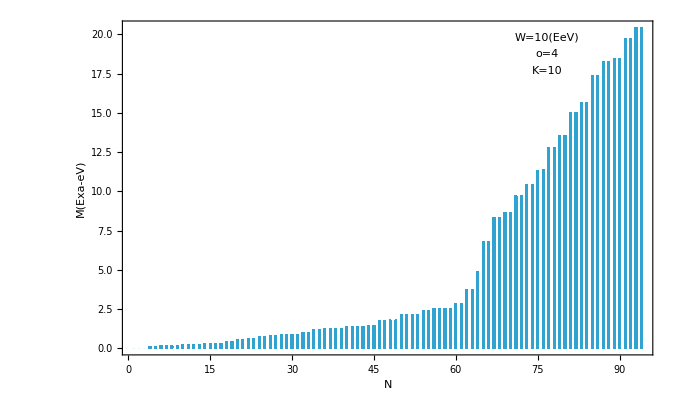

```mathematica
DiscretePlot[Ev1[[i]],{i,1,2*K*o+4},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","M(Exa-eV)"},LabelStyle->Directive[Bold, Medium],Epilog->{Text["o=4",Scaled[{0.8,0.90}]],Text["W=10(EeV)",Scaled[{0.8,0.95}]],{Text["K=10",Scaled[{.8,.85}]]}}]
```

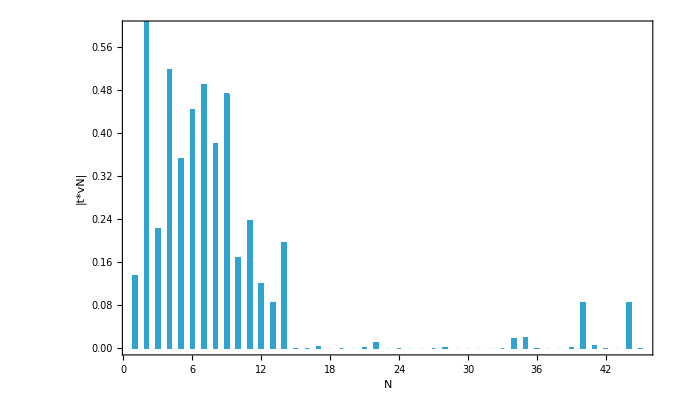

```mathematica
DiscretePlot[Abs[tvNF[[1,i]]],{i,1,K*o},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","|t*vN|"},LabelStyle->Directive[Bold, Medium],Epilog->{}]
 (* Plot of interaction term t^1*Subscript[v, N,n]^α for neutrino 1. Here first K terms correspond to same generation then next K terms correspond to other generation. *)
```

```mathematica
DiscretePlot[Abs[tvNF[[2,i]]],{i,1,K*o},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","|t*vN|"},LabelStyle->Directive[Bold, Medium],Epilog->{}] (* Plot of interaction term t^2*Subscript[v, N,n]^α for neutrino 2. Here first K terms correspond to same generation then next K terms correspond to other generation. *)
```

-Graphics-

```mathematica
DiscretePlot[Abs[tvNF[[3,i]]],{i,1,K*o},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"N","|t*vN|"},LabelStyle->Directive[Bold, Medium],Epilog->{}] (* Plot of interaction term t^3*Subscript[v, N,n]^α for neutrino 3. Here first K terms correspond to same generation then next K terms correspond to other generation. *)
```

-Graphics-